```mathematica
f[x_]:=(4275)*((Sin[Pi*0.1*Sin[(x-4)/50]/(0.000546)]*(0.000546/(Pi*0.1*Sin[(x-4)/50])))^2)*(Cos[Pi*0.406*Sin[(x-4)/50]/0.000546]^2);
Table[f[x],{x,0,8,0.05}]
```

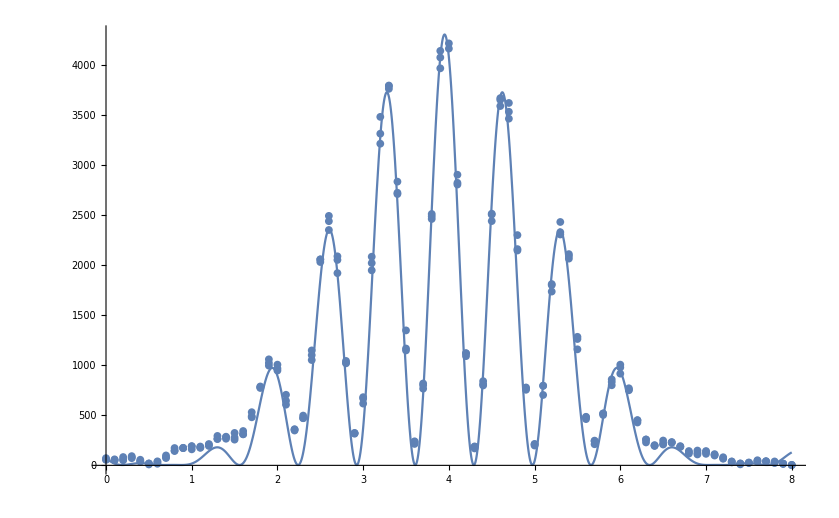

```mathematica
data = Import["/Users/emulder/GitHub/PhotonInterferenceLab/Analysis/445mmAll.csv"];
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/500]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/500])))^2)*(Cos[Pi*d*Sin[(x-x0)/500]/lambda]^2)+c;
I0 = 4300;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
fit = Plot[g[x],{x,0,8}];
dataPlot = ListPlot[data,PlotMarkers->{Automatic,8}];
Show[fit,dataPlot]
```